# Extending SML Package - Hierarchical Solver for the Stationary Distribution on the boundaries of a Markov One-step Process

## Method

## Functions

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
DiscreteZero[vecXY_List]:=Module[
{
vecY=vecXY[[All,2]],(*list of y values*)
vecSI={{0,0}},vecSIZerosOut={{0,0}},splitVecSI={{{0,0}}},crossingIndexs={{0}},x={0.},dx={0.},CloseIndex={0},ifStable={False},dxtemp=0.,xtemp=0.
},

vecSI=Transpose@{Sign[vecY],Range[Length[vecY]]};(*List of signal (-1,0,1) for each index*)
vecSIZerosOut=Select[vecSI,First[#]!=0&];(*Filter out zeros: List of signal (-1,1) for each index*)
splitVecSI=Split[vecSIZerosOut,First[#1]==First[#2]&];(*Group into positive values of y and negative values*)
crossingIndexs=Transpose@{Most[Max[#[[All,2]]]&/@splitVecSI],Rest[Min[#[[All,2]]]&/@splitVecSI]};(*index of transitions from positive to negative values (or vice versa)*)
If[Length[crossingIndexs]>0,
ifStable=Table[If[vecSI[[crossingIndexs[[i,1]],1]]>0,True,False],{i,1,Length[crossingIndexs]}];(*Check if it is a stable point of not: List of True and False for each transition*)
{dx,x,CloseIndex}=Transpose@
Table[If[ifStable[[i]],
{
	dxtemp=(vecXY[[crossingIndexs[[i,2]],2]]-vecXY[[crossingIndexs[[i,1]],2]])/(vecXY[[crossingIndexs[[i,2]],1]]-vecXY[[crossingIndexs[[i,1]],1]]),
	xtemp=vecXY[[crossingIndexs[[i,1]],1]]-vecXY[[crossingIndexs[[i,1]],2]]dxtemp,
	Ordering[Abs[vecXY[[All,1]]-xtemp],1][[1]]
}

,{0.,0.,0}],{i,1,Length[crossingIndexs]}];

Select[Select[Transpose@{x,dx,CloseIndex,ifStable},#[[-1]]&][[All,1;;-2]],#[[-1]]!=1&&#[[-1]]!=Length[vecY]&],
{}]
];
```

```mathematica
DiscreteZero2[vecXY_List]:=With[{initSize=5},
Module[{x=Table[0.,{i,1,initSize}],dx=Table[0.,{i,1,initSize}],CloseIndex=Table[0,{i,1,initSize}],vsize=initSize,nzeros=0},
Do[
If[vecXY[[i,2]]>= 0&&vecXY[[i+1,2]]<= 0,
If[nzeros+1>vsize,
AppendTo[x,Table[0.,{i,1,initSize}]];
AppendTo[dx,Table[0.,{i,1,initSize}]];
AppendTo[CloseIndex,Table[0,{i,1,initSize}]];
vsize+=initSize;
];
nzeros++;

dx[[nzeros]]=(vecXY[[i+1,2]]-vecXY[[i,2]])/(vecXY[[i+1,1]]-vecXY[[i,1]]);x[[nzeros]]=vecXY[[i,1]]-vecXY[[i,2]]dx[[nzeros]];CloseIndex[[nzeros]]=If[Abs[x[[nzeros]]-vecXY[[i,1]]]<Abs[x[[nzeros]]-vecXY[[i+1,1]]],i,i+1];
];
,{i,1,Length[vecXY]-1}];

If[nzeros>0,
Transpose@{x[[1;;nzeros]],dx[[1;;nzeros]],CloseIndex[[1;;nzeros]]},
{}]
]
];
```

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
TransitionsPairs::difdimensions="The lenght of the first list, `1`, is equal to that of the second, `2`.";
TransitionsPairs[Tp_List,Tm_List]:=If[Length[Tp]==Length[Tm],
With[{Z=Length[Tp]-1},Module[{zeros=DiscreteZero2[Transpose@{Range[0,Z]/Z,Tp-Tm}], CoIindex={1,Z+1},Pp=1.,Pm=1.},
If[Length[zeros]>0,
CoIindex=Flatten@Insert[CoIindex,zeros[[All,-1]],2] ;
];

{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
Flatten[{0.,zeros[[All,1]],1.}],(*Point position from 0 to 1*)
Flatten[{1.,zeros[[All,2]],1.}],(*Drift derivative*)
Flatten[{1.,Table[(Tm[[CoIindex[[i]]]]+Tp[[CoIindex[[i]]]])/(2Z),{i,2,Length[CoIindex]-1}],1.}](*Diffusion*)
},
SparseArray[Flatten[Table[
(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1+Pp Tm[[k]]/Tp[[k]];,{k,CoIindex[[i]]+1,CoIindex[[i+1]]-1}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1+Pm Tp[[k]]/Tm[[k]];,{k,CoIindex[[i+1]]-1,CoIindex[[i]]+1,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)
{{i,i+1}-> Tp[[CoIindex[[i]]]]/Pp,{i+1,i}->Tm[[CoIindex[[i+1]]]]/Pm}
,{i,1,Length[CoIindex]-1}]]]
}
]]
,Message[TransitionsPairs::difdimensions,Dimensions[Tp],Dimensions[Tm]]];
```

```mathematica
TransitionsPairs[{0.2,0.55,0.4,0.1},{0.1,0.5,0.35,0.05}]
```

{{{1,0.,1.,1.},{4,1.,1.,1.}},SparseArray[<2>, {2, 2}]}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
StatDESML[s_,T_,Z_,par_List]:=
Module[{CoIp=Table[{{0}},{i,1,Binomial[s,2]}],normp=Table[{{0}},{i,1,Binomial[s,2]}],ρ=Table[{{0}},{i,1,Binomial[s,2]}],CoINorm={{{0,0,0},{0.,0.}}},pair=0,CoIIndex={0},zeros={{0.,0.,0}},CoI={{0}},TMat, vec={0.}},

Do[
pair++;
{zeros,ρ[[pair]]}=TransitionsPairs[Table[T[s1,s2,i,Z,par],{i,0,Z}],Table[T[s2,s1,i,Z,par],{i,0,Z}]];
CoIIndex=zeros[[All,1]];

normp[[pair]]=zeros[[All,{3,4}]];
CoIp[[pair]]=Transpose@{Table[
SparseArray[{s1->( CoIIndex[[i]]-1),s2->(Z-(CoIIndex[[i]]-1))},{s}]
,{i,1,Length[CoIIndex]}],
zeros[[All,{3,4}]]};

,{s1,1,s},{s2,s1+1,s}];


CoINorm=DeleteDuplicatesBy[First]@(Flatten[#,1]&@CoIp//Normal);
CoI=CoINorm[[All,1]];

TMat=Plus@@(Module[{set},(set=Flatten@((Position[CoI,#[[1]]//Normal]&)/@CoIp[[#]]);
SparseArray[{({i_,j_}/;(MemberQ[set,i]&&MemberQ[set,j])):>ρ[[#]][[Position[set,i][[1,1]],Position[set,j][[1,1]]]]},{1,1}Length@CoI])&/@Range[Binomial[s,2]]]);


Do[
TMat[[i,i]]=-Total[TMat[[i,All]]];
,{i,1,Length@TMat}];

vec=NullSpace[Transpose@TMat][[-1]];


Do[
If[CoINorm[[i,2,1]]<0,vec[[i]]*=Z √(2π CoINorm[[i,2,2]]/(-CoINorm[[i,2,1]]))];
,{i,1,Length@vec}];

{CoI,vec/Total[vec]}
];
```

## Using the function

lalala game theory

```mathematica
Δf[i_,Z_,is_,β_]:=β(i-is)/Z;
Tp[i_,Z_,is_,β_,μ_]:=(Z-i)/Z(i/(Z-1)1/(1+ⅇ^(-Δf[i,Z,is,β]))(1-μ)+μ);
Tm[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T[fs_,ts_,k_,Z_,par_List]:=Module[{β=par[[1]],μ=par[[2]],is=par[[3]]},
If[fs==1&&ts==2,
Tp[k,Z,is,β,μ],
If[fs==2&&ts==1,
Tm[k,Z,is,β,μ],
If[fs==1&&ts==3,
Tp[k,Z,is,β,μ],
If[fs==3&&ts==1,
Tm[k,Z,is,β,μ],
If[fs==2&&ts==3,
Tp[k,Z,is,β,μ],
If[fs==3&&ts==2,
Tm[k,Z,is,β,μ],
1-3Tp[k,Z,is,β,μ]-3Tm[k,Z,is,β,μ]
]]]]]]];
```

```mathematica
With[{Z=50,β=-10.,is=35},
Print[StatDESML[2,T,Z,{Z,1.,is}]];
]
```

{{{0,50},{25,25},{50,0}},{8.9263×10^-16,1.,0.}}

{{{0,50},{25,25},{50,0}},{8.9263×10^-16,1.,0.}}

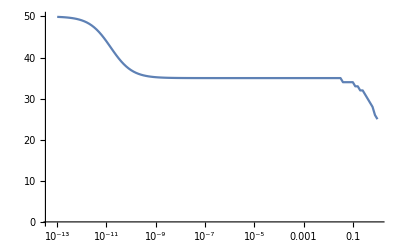

```mathematica
plotA=With[{Z=50,β=-10.,is=35},
Print[StatDESML[2,T,Z,{β,1,is}]];
Monitor[data=Table[
Flatten@{μ,Plus@@Times@@StatDESML[2,T,Z,{β,μ,is}]}
,{μ,10.^FindDivisions[Log10[{10^-13,10^0}],150]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]
]
```

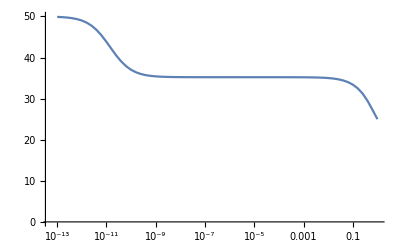

```mathematica
plotB=With[{Z=50,β=-10.,is=35},
Module[{Mat,vec},

Monitor[

data=Table[

Mat=SparseArray[{{i_,j_}/;j==i+1:>Tp[i-1,Z,is,β,μ],{i_,j_}/;j==i-1:>Tm[i-1,Z,is,β,μ],{i_,j_}/;j==i:>1-If[i<Z+1,Tp[i-1,Z,is,β,μ],0]-If[i>1,Tm[i-1,Z,is,β,μ],0]},{Z+1,Z+1}];
vec=Eigenvectors[Transpose[Mat],1,Method->{"Arnoldi", "Shift"->1.0000000001}][[1]];
vec=vec/Total[vec];
Flatten@{μ,(Plus@@Times@@{vec,Range[0,Z]})}
,{μ,10.^FindDivisions[Log10[{10^-13,10^-0}],100]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]




]
]
```